/Users/jacobsnyder/Documents/CALTECH/Sophomore/Term 2/Ma3

0.496576

0.289859

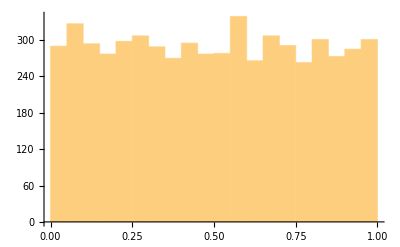

Set2Problem6Plot1.pdf

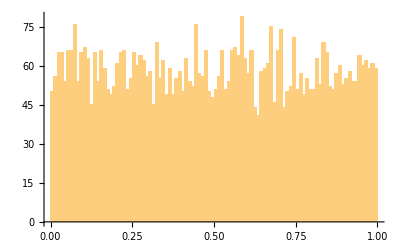

Set2Problem6Plot2.pdf

```mathematica
SetDirectory["/Users/jacobsnyder/Documents/CALTECH/Sophomore/Term 2/Ma3"]
a=Flatten[Import["Random32.txt","Table"]];
Mean[a]
StandardDeviation[a]
g=Histogram[a]
Export["Set2Problem6Plot1.pdf",g]
g=Histogram[a,{0,1,0.01}]
Export["Set2Problem6Plot2.pdf",g]
```

```mathematica
Uniform[0,1]
```

Uniform[0,1]

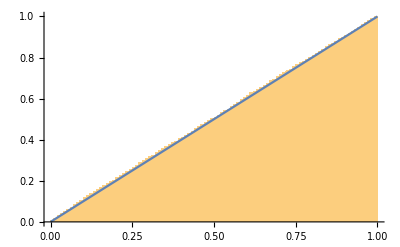

Set2Problem6Plot3.pdf

```mathematica
g=Histogram[a,{0,1,0.01},"CDF"];
g1=Plot[x,{x,0,1}];
Show[g,g1]
Export["Set2Problem6Plot3.pdf",g]
```